## MKP v 2D, priehyb membrany

Fyzikalne parametre

```mathematica
Emodul=0.01 10^9;(*Youngov modul pruznosti, guma [Pa]*)
ν=0.5;(*Poissonovo cislo, guma*)
d=0.001;(*hrubky membrany [m]*)
ρ=1100;(*hustota gumy [kg/m^3]*)
ρS=ρ d;(*plosna hustota membrany [kg/m^2]*)
ρSNEH=0.5 1000;(*hustota snehu [kg/m^3]*)
dSneh=1;(*vyska snehu [m]*)
gg=10;(*gravitacne zrychlenie [m/s^2]*)
a[{x_,y_}]=1;(*Emodul/(2(1+ν))d*)(*tuhost membrany [Pa m]*)
f[{x_,y_}]=0;(*-ρS gg-ρSNEH dSneh gg*)(*intenzita vonkajsich sil, vlastna tiaz + tiaz snehu [N/m^2] *)
```

Geometricke parametre

```mathematica
sirka=2;vyska=1.5;(*rozmery obdlznika*)
x1=0;x2=x1+sirka;
y1=0;y2=y1+vyska;
ΩΩ=Polygon[{{x1,y1},{x2,y1},{x2,y2},{x1,y2}}];(*vypoctova oblast*)
Γ1=Line[{{x1,y1},{x2,y1}}];(*1. cast hranice*)
Γ2=Line[{{x2,y1},{x2,y2}}];(*2. cast hranice*)
Γ3=Line[{{x2,y2},{x1,y2}}];(*3. cast hranice*)
Γ4=Line[{{x1,y2},{x1,y1}}];(*4. cast hranice*)
Γ=RegionUnion[Γ1,Γ2 ,Γ3,Γ4];(*hranica*);
```

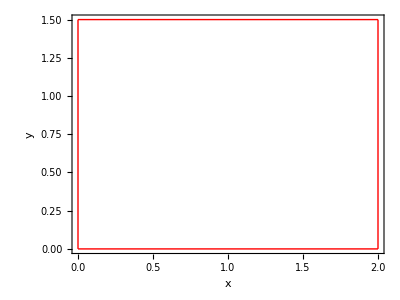

```mathematica
Γplot=RegionPlot[Γ,BoundaryStyle->{Thick,Red},AspectRatio->Automatic,FrameLabel->{Style[x,Large],Style[y,Large]}]
```

Parametre okrajovych podmienok (Dirichlet)

```mathematica
g1[{x_,y_}]=Sin[Pi (x-x1)/(x2-x1)]; (*okrajova podmienka na Γ1*)
g2[{x_,y_}]=0.5Sin[3Pi (y-y1)/(y2-y1)]; (*okrajova podmienka na Γ2*)
g3[{x_,y_}]=(*Sin[Pi (x-x1)/(x2-x1)]*)x(2-x); (*okrajova podmienka na Γ3*)
g4[{x_,y_}]=Sin[Pi (y-y1)/(y2-y1)]; (*okrajova podmienka na Γ4*);
```

```mathematica
(*vykreslenie okrajovych podmienok*)
g1plot=ParametricPlot3D[{x,y1,g1[{x,y1}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g2plot=ParametricPlot3D[{x2,y,g2[{x2,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g3plot=ParametricPlot3D[{x,y2,g3[{x,y2}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g4plot=ParametricPlot3D[{x1,y,g4[{x1,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
```

```mathematica
gplot=Show[g1plot,g2plot,g3plot,g4plot,PlotRange->All]
```

-Graphics3D-

Presne riesenie (plati pre g-cka rovne sinusom - s akymkolvek poctom “kopcekov” a a=1, f=0)

```mathematica
uA[{x_,y_}]=
g1[{x,y1}]Sinh[Pi/(x2-x1)(y2-y)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g2[{x2,y}]Sinh[Pi/(y2-y1)(x-x1)]/Sinh[Pi(x2-x1)/(y2-y1)]+
g3[{x,y2}]Sinh[Pi/(x2-x1)(y-y1)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g4[{x1,y}]Sinh[Pi/(y2-y1)(x2-x)]/Sinh[Pi(x2-x1)/(y2-y1)]
```

0.0303362 Sin[2.0944 y] Sinh[2.0944 (2-x)]+0.0151681 Sin[6.28319 y] Sinh[2.0944 x]+0.191279 Sin[(π x)/2] Sinh[1/2 π (1.5-y)]+0.191279 (2-x) x Sinh[(π y)/2]

```mathematica
uAplot3D=Plot3D[uA[{x,y}],{x,y}∈ΩΩ,AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]},BoxRatios->Automatic,PlotStyle->{Red,Opacity[0.5]},PlotRange->All]
```

-Graphics3D-

MKP, diskretizacia oblasti

```mathematica
nx=6;(*pocet dielikov v smere x*)
ny=4;(*pocet dielikov v smere y*)
hx=sirka/nx;hy=vyska/ny;(*dlzka dielokov v smere x/y*)
X=Table[{x1+i*hx,y1+j*hy},{j,0,ny},{i,0,nx}];(*globalne uzlove body*)
X=Flatten[X,1];
n=Length[X];(*pocet neznamych globalnych uzlovych hodnot*)
nE=nx*ny*2;  (*pocet elementov*)
```

```mathematica
B=Table[{0,0,0},nE];(*B(e,i) = globalne cislo i-teho bodu na e-tom elemente *)
idx=1;
For[i=1,i≤nx*ny+ny-1,If[Mod[i+1,nx+1]==0,i=i+2,i++],
B[[idx]]={i,i+1,i+nx+2};
B[[idx+1]]={i,i+nx+2,i+nx+1};
idx=idx+2;
]
```

```mathematica
Ω=Table[Triangle[X⟦B⟦e⟧⟧],{e,1,nE}];(*elementy*)
```

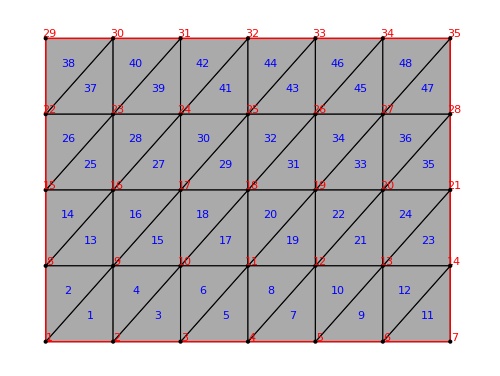

```mathematica
Xplot=Graphics[Point[X]];(*vykreslenie uzlovych bodov*)
XIDplot=Graphics[{Red,Table[Text[i,X⟦i⟧+{0.02,0.02}],{i,1,n}]}];(*vykreslenie cisel uzlovych bodov*)
EdgePlot=Graphics[{FaceForm[None],EdgeForm[Black],Ω}];(*vykreslenie hran*)
ElemPlot=Graphics[{FaceForm[Lighter[Gray]],EdgeForm[Black],Ω}];(*vykreslenie elementov*)
ElemPlotIDplot=Graphics[{Blue,Table[Text[e,Mean[X⟦B⟦e⟧⟧]],{e,1,nE}]}];(*vykreslenie cisel elementov*)
Show[ElemPlot,Γplot,ElemPlotIDplot,Xplot,XIDplot,ImageSize->500]
```

MKP, diskretizacia okrajovej podmienky

```mathematica
dirichlet=Table[False,{n}];
```

```mathematica
For[i=1,i≤nx+1,i++,
For[j=1,j≤ny+1,j++,
If[i==1||i==nx+1||j==1||j==ny+1,
dirichlet[[(j-1)*(nx+1)+i]]=True;,
];(* dirichlet(i) = True, ak je X(i) na hranici oblasti*)
];
]
g=Table[If[dirichlet[[i]],
If[X[[i]]∈Γ1,g1[X[[i]]],
If[X[[i]]∈Γ2,g2[X[[i]]],
If[X[[i]]∈Γ3,g3[X[[i]]],
If[X[[i]]∈Γ4,g4[X[[i]]]]]]],0],{i,1,n}];
g[[18]]=1.3;
dirichlet[[18]]=True;
```

MKP, zostrojenie linearnych aproximacnych funkcii

```mathematica
For[e=1,e<=nE,e++,
x1=X[[B[[e,1]],1]];
x2=X[[B[[e,2]],1]];
x3=X[[B[[e,3]],1]];
y1=X[[B[[e,1]],2]];
y2=X[[B[[e,2]],2]];
y3=X[[B[[e,3]],2]];

α1=x2*y3-x3*y2;
α2=x3*y1-x1*y3;
α3=x1*y2-x2*y1;
β1=y2-y3;
β2=y3-y1;
β3=y1-y2;
γ1=-(x2-x3);
γ2=-(x3-x1);
γ3=-(x1-x2);

DD=α1+α2+α3;
ψ[e,1]=(α1+β1*x+γ1*y)/DD;
ψ[e,2]=(α2+β2*x+γ2*y)/DD;
ψ[e,3]=(α3+β3*x+γ3*y)/DD;
]
```

MKP, zostrojenie lokalnych matic a pravych stran

```mathematica
LokK=Table[0,nE,3,3];
LokF=Table[0,nE,3];
```

```mathematica
AbsoluteTiming[
Do[
LokK⟦e⟧=Table[Integrate[a[{x,y}]*(D[ψ[e,i],x]*D[ψ[e,j],x]+D[ψ[e,i],y]*D[ψ[e,j],y]),{x,y}∈Ω[[e]]],{i,1,3},{j,1,3}];
LokF⟦e⟧=Table[Integrate[f[{x,y}]*ψ[e,i],{x,y}∈Ω[[e]]],{i,1,3}]
,{e,1,nE}]
]
```

{2.8905,Null}

```mathematica
LokK⟦1⟧//MatrixForm;
LokF⟦1⟧//MatrixForm;
```

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
GlobK=Table[0,n,n];
GlobF=Table[0,n];
For[e=1,e≤nE,e++,
For[i=1,i≤3,i++,
GlobF[[B[[e,i]]]]+=LokF[[e,i]];
For[j=1,j≤3,j++,
GlobK[[B[[e,i]],B[[e,j]]]]+=LokK[[e,i,j]]
];
];
]
```

```mathematica
GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, zahrnutie okrajovych podmienok

```mathematica
For[e=1,e≤n,e++,
If[dirichlet[[e]],
GlobF[[e]]=g[[e]];
GlobK[[e]]=Table[0,n];
GlobK[[e,e]]=1;
,]
]
```

```mathematica
GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

```mathematica
U=LinearSolve[GlobK,GlobF]//N;(*riesenie systemu*)
```

```mathematica
XU=Table[Append[X⟦i⟧,U⟦i⟧],{i,1,n}];(*konstrukcia 3D bodov pre vykreslenie riesenia ako grafu v 3D*)
```

```mathematica
(* konstrukcia riesenia na elementoch*)
Do[
Do[
u[e,i]=U⟦B⟦e,i⟧⟧
,{i,1,3}];
UNlok[e][{x_,y_}]=∑_(j=1)^3 u[e,j]*ψ[e,j];
,{e,1,nE}];
(* konstrukcia celkoveho MKP riesenia*)
UNglob[{x_,y_}]=Piecewise[Table[{UNlok[e][{x,y}],{x,y}∈Ω⟦e⟧},{e,1,nE}]];
(*dalej sa nepouziva, lebo vykreslovanie aj vypocet chyby cez Piecewise trva dlho*)
```

```mathematica
AbsoluteTiming[
UNlokPlot[e_]:=Plot3D[UNlok[e][{x,y}],{x,y}∈Ω⟦e⟧,PlotPoints->2,AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
Uplot3D=Show[gplot,Table[UNlokPlot[e],{e,1,nE}],BoxRatios->Automatic];
Uplot3Dpoints=ListPointPlot3D[Table[XU⟦i⟧,{i,1,n}],AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]},PlotStyle->{Blue,PointSize[0.02]}];(*vykreslenie uzlovych hodnot*)
Uplot3Dedges=Graphics3D[{FaceForm[None],EdgeForm[{Thick,Black}],Table[Triangle[XU⟦B⟦e⟧⟧],{e,1,nE}]}];(*vykreslenie hran trojuholnikov*)
UNlokContourPlot[e_]:=ContourPlot[UNlok[e][{x,y}],{x,y}∈Ω⟦e⟧,FrameLabel->{Style[x,Large],Style[y,Large]},Contours->Table[i/20,{i,0,20}],AspectRatio->Automatic,ColorFunction->(ColorData["TemperatureMap",#]&),ColorFunctionScaling->False];
UcontourPlot=Show[Table[UNlokContourPlot[e],{e,1,nE}]];
]
```

{3.47817,Null}

```mathematica
Show[Uplot3D,(*uAplot3D,*)Uplot3Dedges,Uplot3Dpoints,gplot,BoxRatios->Automatic,ImageSize->500]
Show[Γplot,UcontourPlot,EdgePlot,ImageSize->500]
```

-Graphics3D-

-Graphics-

MKP, vypocet chyb a EOC

```mathematica
L2Chyba=Sqrt[∑_(e=1)^nE Integrate[(UNlok[e][{x,y}]-uA[{x,y}])^2,{x,y}∈Ω[[e]]]]
```

0.316136

```mathematica
EnergetickaChyba=Sqrt[∑_(e=1)^nE Integrate[a[{x,y}]*Norm[Grad[UNlok[e][{x,y}],{x,y}]-Grad[uA[{x,y}],{x,y}]]^2,{x,y}∈Ω[[e]]]]
```

1.62679

```mathematica
(* s=1, chyby pre stale hustejsiu siet - vzdy zmensim hx a hy o polovicu*)
L2chyby={0.08276400325531788,0.022503140607902906,0.005774772946876591,0.0014537081297702587,0.0003640646493169061};
ENchyby={0.6718168322795235,0.3514859651458633,0.1779114095210851,0.08923516238560937,0.04465279086232095};
```

```mathematica
(* EOC *)
L2EOC=Table[Log2[L2chyby[[i]]/L2chyby[[i+1]]],{i,1,Length[L2chyby]-1}];
ENEOC=Table[Log2[ENchyby[[i]]/ENchyby[[i+1]]],{i,1,Length[ENchyby]-1}];
```

```mathematica
labels={{"nx","ny","n","nE","L2 chyba","EOC L2","Energ. chyba","EOC Energ."}};
table=Table[{3 2^(i-1),2 2^(i-1),(3 2^(i-1)+1)(2 2^(i-1)+1),12 2^(2(i-1)),AccountingForm[L2chyby⟦i⟧,4],If[i==1,"",AccountingForm[L2EOC⟦i-1⟧,4]],AccountingForm[ENchyby⟦i⟧,4],If[i==1,"",AccountingForm[ENEOC⟦i-1⟧,4]]},{i,1,Length[L2chyby]}];
```

```mathematica
plotTable=Grid[Join[labels,table],Frame->All,Alignment->{{Right,Left,Left,Left,Left}},Background->{{Yellow,Yellow,Yellow,Yellow,None},{Yellow,None}}]
```

nx | ny | n | nE | L2 chyba | EOC L2 | Energ. chyba | EOC Energ.
3 | 2 | 12 | 12 | 0.08276 |  | 0.6718 | 
6 | 4 | 35 | 48 | 0.0225 | 1.879 | 0.3515 | 0.9346
12 | 8 | 117 | 192 | 0.005775 | 1.962 | 0.1779 | 0.9823
24 | 16 | 425 | 768 | 0.001454 | 1.99 | 0.08924 | 0.9955
48 | 32 | 1617 | 3072 | 0.0003641 | 1.997 | 0.04465 | 0.9989